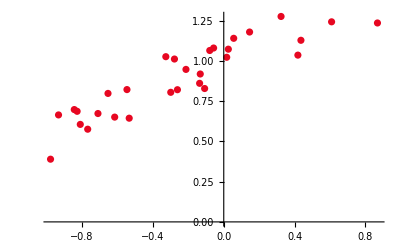

```mathematica
(*导入数据，第一列为x坐标，第二列为y坐标*)
Clear[data];
data=N[Import["E:\\study_materials\\MachineLearning\\HW1\\data.txt","Data"],15];
(*绘制原始数据点图*)
img=ListPlot[data,PlotStyle->ColorData[3,"ColorList"]]
```

```mathematica
(*提取x,y坐标*)
x=data[[All,1]];
y=data[[All,2]];
```

二范数误差error=0.531194876522673
w0=1.00038680662317
w1=0.430838344703966

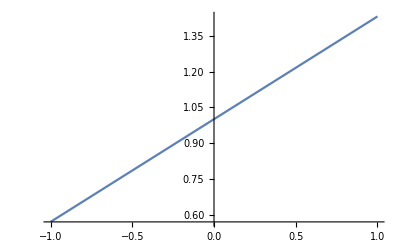
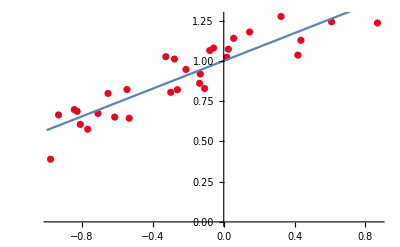
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*线性回归*)
(*生成系数矩阵*)
A1=Table[{1,data[[i,1]]},{i,1,Length[data]}];
(*求解系数*)
wlinear=Inverse[Transpose[A1].A1].(Transpose[A1].y);
(*绘制模型图像*)
img1=Plot[wlinear[[1]]+wlinear[[2]]*x,{x,-1,1}];
(*计算二范数误差*)
y1=wlinear[[1]]+wlinear[[2]]*x;
error1=Sqrt[Sum[(y1[[i]]-y[[i]])^2,{i,1,Length[y]}]];
(*输出相关结果*)
Print["二范数误差error=",NumberForm[error1,15],"\n","w0=",NumberForm[wlinear[[1]],15],"\n","w1=",NumberForm[wlinear[[2]],15]]
{img,img1,Show[img,img1]}
```

二范数误差error=0.492436111120306
w0=1.02956837465647
w1=0.386143334032323
w2=-0.142151113086161

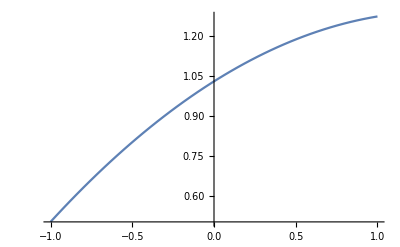
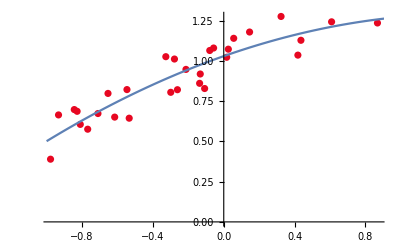
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*二次回归*)
(*生成系数矩阵*)
A1=Table[{1,data[[i,1]],data[[i,1]]^2},{i,1,Length[data]}];
(*求解系数*)
wquard=Inverse[Transpose[A1].A1].(Transpose[A1].y);
(*绘制模型图像*)
img2=Plot[wquard[[1]]+wquard[[2]]*x+wquard[[3]]*x^2,{x,-1,1}];
(*计算二范数误差*)
y2=wquard[[1]]+wquard[[2]]*x+wquard[[3]]*x^2;
error2=Sqrt[Sum[(y2[[i]]-y[[i]])^2,{i,1,Length[y]}]];
(*输出相关结果*)
Print["二范数误差error=",NumberForm[error2,15],"\n","w0=",NumberForm[wquard[[1]],15],"\n","w1=",NumberForm[wquard[[2]],15],"\n","w2=",NumberForm[wquard[[3]],15]]
{img,img2,Show[img,img2]}
```

可以看到，二次模型更好的回归拟合出更贴近原数据，从二范数的误差结果来看，也是二次模型更为适合一些。